```mathematica
<<UtilityManager`

<<PrettyTheme`
$PlotTheme="Academic";
```

```mathematica
momentsOfBetaFromMomentsOfX[h_,a_,momentsOfX_,q_]:=h^q(1+ Sum[(a q)^k/(k!)momentsOfX[[k]],{k,1,Length[momentsOfX]}])/.q->1;

SingleNeuronTheoryMomentsBetaX[τ_,h_,a_,inputRates_,inputWeights_,orderUpTo_]:=Module[
{rates,weights,M,meshNum,du,uList,
getId,getIdRange,V,VInt,Vv,
q0,qList,qLog,
diff,vv,RSym,R,
qLogDerivatives,qInvDerivatives,uInvDerivatives,
Q0,complexInfInQ0,indeterminedInQ0,newM,Q0Derivatives,
QArray,iteration,QnaList,padeSums,β,momentsOfX,
nth,mth,u,n,v,k,x,y,
padeSumsBeta,momentsOfBeta,
truncateUponNonNumber
},
(*Select the non-zero synaptic strength inputs*)
{rates,weights}=Transpose@Select[Thread[{inputRates,inputWeights}],N[#[[2]]]≠0.&];

(*If all input rates are zero, out base rate h*)
If[
Length[Cases[rates,0.]]==Length[rates],
Message[SingleNeuronTheoryPade::zero];
Return[h];
];

(*`M` determines the max iterations*)
M=50;
(*`meshNum` determines the number of meshes in each interval of length `a`*)
meshNum=500;
(*`du` is the mesh length*)
du=a/meshNum;
(*`uList` is the array of u points in interval [0, (M+1+Order) a]*)
uList=Range[0,a*(M+1+orderUpTo),du];
(*Auxiliary functions to get indices at integer multiple of `a`*)
getId[nth_]=nth*meshNum+1;
getIdRange[nth_,mth_]=Span[nth*meshNum+1,mth*meshNum];

(*V is ensured to be non-zero here*)
(*V(u)*)
V[0,u_]=rates.(Exp[weights u]-1);
(*n-th derivatives of V(u), n≥1*)
V[n_,u_]/;n≥1=rates.(weights^n Exp[weights u]);
(*Indefinite integral of V(u)*)
VInt[v_]=rates.(ExpIntegralEi[weights v]-Log[v]);
(*n-th derivatives of V(u)/u*)
Vv[n_,0|0.]=V[n+1,0]/(n+1);
Vv[n_,u_]=(-1)^(n+1)/(u)^(n+1)(rates.Re[Gamma[n+1,0,-weights*u]]);

(*Compute `q` function at u points in [0, (M+1+Order) a]*)
q0=Exp[NIntegrate[V[0,v]/v,{v,0,a}]];
qList=Exp[VInt[a]-VInt[Rest@uList]];
PrependTo[qList,q0];
(*ASSERT: `qList` has same length as `uList`*)
Assert[Length[qList]==Length[uList]];

(*n-th (n≥1) derivatives of log(q(u))*)
qLog[n_,0|0.]=-Vv[n-1,0];
qLog[n_,u_]=-Vv[n-1,u];

(*derivative rules*)
diff[vv[k_,u_]]=vv[k+1,u];
diff[-x_vv]=-diff[x];
diff[x_+y_]=diff[x]+diff[y];
diff[x_vv^n_Integer]:=n x^(n-1) diff[x];
diff[x_vv y_vv]=x diff[y]+y diff[x];
diff[x_ y_vv]=x diff[y];
diff[1]=0;
(*r_k+1 = r_k' + vv r_k*)
RSym[0,u_]=1;
RSym[k_,u_]:=diff[RSym[k-1,u]]+vv[0,u]*RSym[k-1,u];
SetAttributes[R,Listable];
(*R_k(u) when u=0*)
R[k_,0|0.]:=R[k,0|0.]=Simplify[RSym[k,u]/.vv[n_,u_]->Vv[n,0]];
Table[R[k,0],{k,0,orderUpTo}]; (*Evaluate to save definitions*)
(*R_k(u) when u≠0*)
R[k_,u_]:=R[k,u]=Simplify[RSym[k,u]/.vv->Vv];
Table[R[k,u],{k,0,orderUpTo}]; (*Evaluate to save definitions*)

(*Compute 1 ~ orderUpTo-th derivatives of Log q(u) at u=(0,1,...,M+1+orderUpTo)a*)
qLogDerivatives=Chop@Table[
qLog[k,#]&/@uList[[;;;;meshNum]],
{k,1,orderUpTo}];
(*Compute 0 ~ (orderUpTo-1)-th derivatives of 1/q(u) at u=(0,1,...,M+1+orderUpTo)a*)
Quiet[qInvDerivatives=Chop@Table[
(R[k,#]&/@uList[[;;;;meshNum]])/qList[[;;;;meshNum]],
{k,0,orderUpTo-1}];];
(*Compute 0 ~ (orderUpTo-1)-th derivatives of 1/u at u=(1,...,M+1+orderUpTo)a*)
uInvDerivatives=Chop@Table[
(-1)^k (k!)/(Rest[uList[[;;;;meshNum]]])^(k+1),
{k,0,orderUpTo-1}];

(*Compute `Q_0 function at u points in [0, (M+OrderUpTo) a]*)
(*Values of `q` in [a, (M+1+OrderUpTo) a] is used*)
Quiet[Q0=(1/qList[[getIdRange[1,M+1+orderUpTo]]]-1);];

(*truncate the list once it reaches Indeterminate or ComplexInfinity*)
truncateUponNonNumber[list_]:=Module[{l=Length[list],id},
id=Min@@Prepend[If[MissingQ[#],l,#[[1]]-1]&/@{
FirstPosition[list,ComplexInfinity],
FirstPosition[list,Indeterminate]
},l];
If[id===0,{},list[[;;id]]]
];

(*Decrease M if there is indetermined*)
complexInfInQ0=FirstPosition[Q0,ComplexInfinity];
indeterminedInQ0=FirstPosition[Q0,Indeterminate];
newM=Min@@Prepend[If[MissingQ[#],M,Ceiling[#[[1]]/meshNum-1]]&/@{complexInfInQ0,indeterminedInQ0},M];
(*Print[newM];*)
M=newM;

(*Compute 0 ~ orderUpTo-th derivatives of Q_0(u) at u=(-1,0,...,M+orderUpTo)a*)
Quiet[Q0Derivatives=Table[
-(Transpose[Reverse[qLogDerivatives[[;;k]]]]*Transpose[qInvDerivatives[[;;k]]]).Binomial[k-1,Range[0,k-1]]
,{k,1,orderUpTo}];];

SetAttributes[QArray,Listable];
(*
QArray[m, k, aN]: 
   `m` the iteration, 
    `k` the derivative order, 
    `aN` the integer multiple of a
*)

(*Q_0(-a)=1/q(0)-1*)
QArray[0,0,-1]=1/q0-1;
Table[QArray[0,0,aN]=Q0[[getId[aN]]],{aN,0,M+orderUpTo-1}];
Table[QArray[0,k,aN]=Q0Derivatives[[k,aN+2]],{aN,-1,M+orderUpTo},{k,1,orderUpTo}];

iteration[Q_,m_]:=
Module[
{QNextIntegrand,QNext,QNextna},
(*Compute the next Q(u)*)
QNextIntegrand=qList[[2;;Length[Q]]]*Q[[2;;]]/uList[[2;;Length[Q]]];
PrependTo[QNextIntegrand,0.];
QNext=Prepend[Accumulate[QNextIntegrand[[meshNum+1;;-2]]],0]*du;
QNext=QNext/qList[[meshNum+1;;meshNum+Length[QNext]]];QNextna=-Total[QNextIntegrand[[2;;meshNum+1]]]*du/q0;
QArray[m,0,-1]=QNextna;
Table[QArray[m,0,aN]=QNext[[getId[aN]]],{aN,0,M+orderUpTo-1-m}];
{QNext,m+1}
];

(*Create definitions for Q_m(u),(m≥1) at 
integer multiple of a points*)
Quiet[NestList[iteration[#[[1]],#[[2]]]&,{Q0,1},M];];

QArray[m_,k_,-1]:=(QArray[m,k,-1]=
-((Reverse[qLogDerivatives[[;;k,1]]]*(QArray[m,Range[0,k-1],-1])).Binomial[k-1,Range[0,k-1]])+QArray[m-1,k,0]/k
);
QArray[m_,k_,aN_]:=(QArray[m,k,aN]=
-(Reverse[qLogDerivatives[[;;k,aN+2]]]*(QArray[m,Range[0,k-1],aN])).Binomial[k-1,Range[0,k-1]]+(Reverse[uInvDerivatives[[;;k,aN+1]]]*(QArray[m-1,Range[0,k-1],aN+1])).Binomial[k-1,Range[0,k-1]]
);

Quiet[QnaList=Table[QArray[Range[0,M],k,-1],{k,0,orderUpTo}];];
padeSums=PadeSummation[#,-h]&/@QnaList;
β=h/(1+padeSums[[1]]);
momentsOfX=β/h*padeSums[[2;;]];

momentsOfBeta={};
If[orderUpTo≥2,
Quiet[padeSumsBeta=Table[QArray[Range[0,M],0,q-1],{q,2,orderUpTo}]];
momentsOfBeta=Table[β h^(q-1)* (1+PadeSummation[truncateUponNonNumber[padeSumsBeta[[q-1]]],-h]),{q,2,orderUpTo}];
];

{Flatten[{β,momentsOfBeta}],momentsOfX}
];



MultiNeuronTheoryMomentsBetaX[τ_,h_,a_,weightMatrix_,orderUpTo_,initialValue_:None]:=Module[
{β,n=Length[weightMatrix],idx,
wmat=zeroDiagonal@weightMatrix},
idx=Table[Cases[Range[1,n],Except[i]],{i,1,n}];
If[initialValue===None,
β=ConstantArray[3N@h,n]+RandomReal[{-0.5,0.5}h,n],
β=initialValue
];
NestWhileList[
(ParallelTable[
SingleNeuronTheoryMomentsBetaX[τ,h,a,#[[idx[[i]],1,1]],wmat[[i,idx[[i]]]],orderUpTo],
{i,1,n}])&,
Transpose[{Transpose[{β,ConstantArray[0,n]}],ConstantArray[{0,0},n]}],
Norm[Flatten[({##}[[-1]]-{##}[[-2]])]]>0.0001h&,
{2,2},100]
];
MultiNeuronHomoTheoryMomentsBetaX[τ_,h_,a_,weightMatrix_,orderUpTo_,groupIDs_,initialValue_:None]:=Module[
{β,n=Length[weightMatrix],n2,repr,idx,idx2,idx2ker,res,
wmat=zeroDiagonal@weightMatrix},
idx=Table[Cases[Range[1,n],Except[i]],{i,1,n}];
repr=Flatten[groupIDs[[All,1]]];
n2=Length[repr];
idx2ker=Normal@SparseArray[Flatten[Table[Thread[groupIDs[[i]]->i],{i,1,n2}]],{n}];
idx2=Table[Drop[idx2ker,{repr[[i]]}],{i,1,n2}];
If[initialValue===None,
β=ConstantArray[3N@h,n2]+RandomReal[{-0.5,0.5}h,n2],
β=initialValue[[repr]]
];
res=NestWhileList[
(Table[
SingleNeuronTheoryMomentsBetaX[τ,h,a,#[[idx2[[i]],1,1]],wmat[[repr[[i]],idx[[repr[[i]]]]]],orderUpTo],
{i,1,n2}])&,
Transpose[{Transpose[{β,ConstantArray[0,n2]}],ConstantArray[{0,0},n2]}],
Norm[Flatten[({##}[[-1]]-{##}[[-2]])]]>0.00001h&,
{2,2},100];
#[[idx2ker]]&/@res
];
```

```mathematica
τ=1.0;h=0.5;a=0.1;
inputRates={0.6};inputWeights={0.8};

orderUpTo=5;
```

```mathematica
momentsTheory1=SingleNeuronTheoryMomentOfX[τ,h,a,inputRates,inputWeights,orderUpTo];
```

```mathematica
momentsSimulation1=SingleNeuronSimulationMomentsOfXTrials[τ,h,a,inputRates,inputWeights,3000,orderUpTo,3];
```

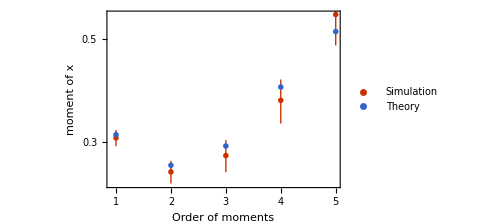

```mathematica
ListLogPlot[
{Around/@momentsSimulation1,Abs@momentsTheory1[[2]]},FrameLabel->{
"Order of moments",
StyledString["moment of `math{`it{x}}"]
},
PlotLegends->{"Simulation","Theory"},
PlotRange->All,
ImageSize->Medium
]
```

```mathematica
testRates1=Table[r,{r,0.1,100000,10000}];
testWeights1=Table[w,{w,0.05,1.0,0.05}];
```

```mathematica
SingleNeuronTheoryPade[1.0,h,a,{#},{0.5}]&/@testRates1
```

```mathematica
SingleNeuronTheoryPade[1.0,h,a,{0.5},{#}]&/@testWeights1
```

```mathematica
momentsVaryRatesSimulation1=Table[SingleNeuronSimulationMomentsOfXTrials[τ,h,a,{r},{0.5},3000,orderUpTo,3],{r,testRates1}];
momentsVaryWeightsSimulation1=Table[SingleNeuronSimulationMomentsOfXTrials[τ,h,a,{0.5},{w},3000,orderUpTo,3],{w,testWeights1}];
```

```mathematica
momentsVaryRatesTheory1=Table[SingleNeuronTheoryMomentOfX[τ,h,a,{r},{0.5},orderUpTo],{r,testRates1}];
momentsVaryWeightsTheory1=Table[SingleNeuronTheoryMomentOfX[τ,h,a,{0.5},{w},orderUpTo],{w,testWeights1}];
```

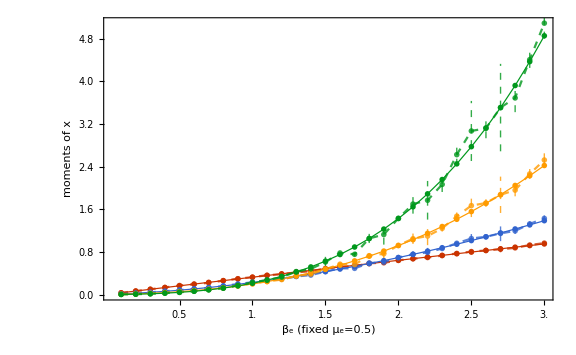

```mathematica
gMomentsCompareVaryRates=ListLinePlot[
Table[Splice[{
momentsVaryRatesTheory1[[All,2,m]],
Around/@(momentsVaryRatesSimulation1[[All,m]])
}],{m,1,4}],
PlotRange->All,
FrameLabel->{"β_e (fixed μ_e=0.5)",StyledString["moments of `math{`it{x}}"]},
FrameTicks->{{Automatic,None},{Table[{i,i/10.},{i,5,30,5}],None}},
PlotStyle->{
{Thickness[0.0015],ColorData[112][1]},{Dashed,Opacity[0.8],ColorData[112][1]},
{Thickness[0.0015],ColorData[112][2]},{Dashed,Opacity[0.8],ColorData[112][2]},
{Thickness[0.0015],ColorData[112][3]},{Dashed,Opacity[0.8],ColorData[112][3]},
{Thickness[0.0015],ColorData[112][4]},{Dashed,Opacity[0.8],ColorData[112][4]}
},
(*PlotLegends->StyledString/@{
"Simulated `math{E(x^1)}","Theoretical `math{E(x^1)}",
"Simulated `math{E(x^2)}","Theoretical `math{E(x^2)}",
"Simulated `math{E(x^3)}","Theoretical `math{E(x^3)}",
"Simulated `math{E(x^4)}","Theoretical `math{E(x^4)}"
},*)
ImageSize->Large
]
```

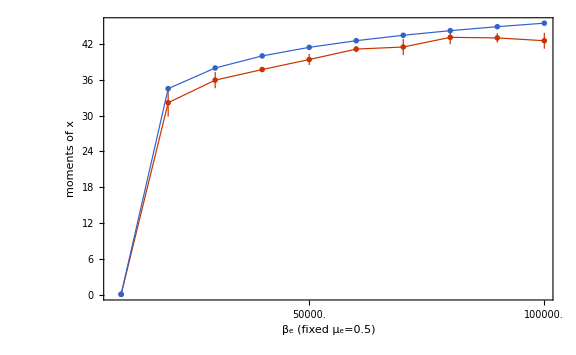

```mathematica
ListLinePlot[
{

Around/@(momentsVaryRatesSimulation1[[All,1]]),
Log[1+0.5 a /h testRates1]/(2a)
(*Around/@(momentsVaryRatesSimulation1[[All,2]])-(Around/@(momentsVaryRatesSimulation1[[All,1]]))^2*)
},
PlotRange->All,
FrameLabel->{"β_e (fixed μ_e=0.5)",StyledString["moments of `math{`it{x}}"]},
FrameTicks->{{Automatic,None},{Table[{i,i*10000.},{i,5,30,5}],None}},
PlotStyle->{
{Thickness[0.0015],ColorData[112][1]},{Thickness[0.0015],ColorData[112][2]},
{Thickness[0.0015],ColorData[112][3]}
},
(*PlotLegends->StyledString/@{
"Simulated `math{E(x^1)}","Theoretical `math{E(x^1)}",
"Simulated `math{E(x^2)}","Theoretical `math{E(x^2)}",
"Simulated `math{E(x^3)}","Theoretical `math{E(x^3)}",
"Simulated `math{E(x^4)}","Theoretical `math{E(x^4)}"
},*)
ImageSize->Large
]
```

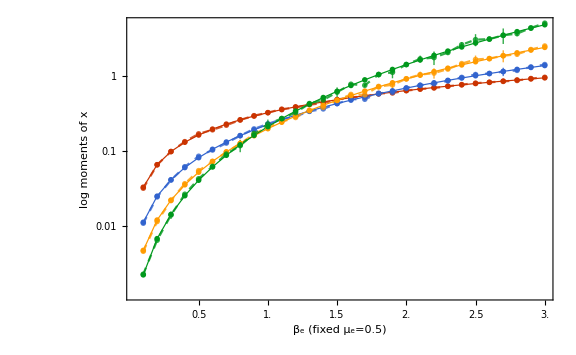

```mathematica
gMomentsCompareVaryRatesLog=ListLogPlot[
Table[Splice[{
momentsVaryRatesTheory1[[All,2,m]],
Around/@(momentsVaryRatesSimulation1[[All,m]])
}],{m,1,4}],
PlotRange->All,
FrameLabel->{"β_e (fixed μ_e=0.5)",StyledString["log moments of `math{`it{x}}"]},
FrameTicks->{{Automatic,None},{Table[{i,i/10.},{i,5,30,5}],None}},
PlotStyle->{
{Thickness[0.0015],ColorData[112][1]},{Dashed,Opacity[0.8],ColorData[112][1]},
{Thickness[0.0015],ColorData[112][2]},{Dashed,Opacity[0.8],ColorData[112][2]},
{Thickness[0.0015],ColorData[112][3]},{Dashed,Opacity[0.8],ColorData[112][3]},
{Thickness[0.0015],ColorData[112][4]},{Dashed,Opacity[0.8],ColorData[112][4]}
},
Joined->True,
(*PlotLegends->StyledString/@{
"Simulated `math{E(x^1)}","Theoretical `math{E(x^1)}",
"Simulated `math{E(x^2)}","Theoretical `math{E(x^2)}",
"Simulated `math{E(x^3)}","Theoretical `math{E(x^3)}",
"Simulated `math{E(x^4)}","Theoretical `math{E(x^4)}"
},*)
ImageSize->Large
]
```

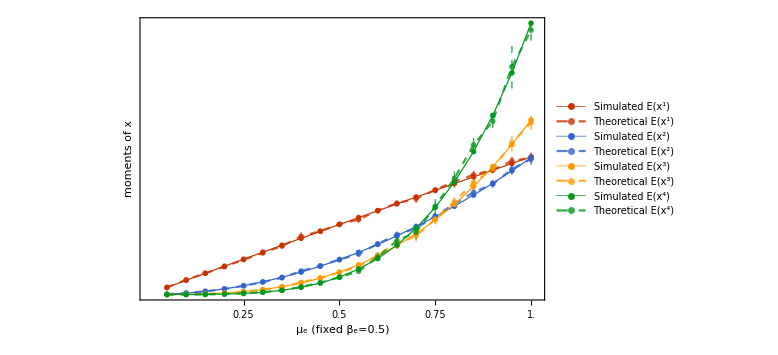

```mathematica
gMomentsCompareVaryWeights=ListLinePlot[
Table[Splice[{
momentsVaryWeightsTheory1[[All,2,m]],
Around/@(momentsVaryWeightsSimulation1[[All,m]])
}],{m,1,4}],
PlotRange->{{0,20.3},All},
FrameLabel->{"μ_e (fixed β_e=0.5)",StyledString["moments of `math{`it{x}}"]},
FrameTicks->{{None,All},{Table[{i,i/20.},{i,5,20,5}],None}},
PlotStyle->{
{Thickness[0.0015],ColorData[112][1]},{Dashed,Opacity[0.8],ColorData[112][1]},
{Thickness[0.0015],ColorData[112][2]},{Dashed,Opacity[0.8],ColorData[112][2]},
{Thickness[0.0015],ColorData[112][3]},{Dashed,Opacity[0.8],ColorData[112][3]},
{Thickness[0.0015],ColorData[112][4]},{Dashed,Opacity[0.8],ColorData[112][4]}
},
PlotLegends->StyledString/@{
"Simulated `math{E(x^1)}","Theoretical `math{E(x^1)}",
"Simulated `math{E(x^2)}","Theoretical `math{E(x^2)}",
"Simulated `math{E(x^3)}","Theoretical `math{E(x^3)}",
"Simulated `math{E(x^4)}","Theoretical `math{E(x^4)}"
},
ImageSize->Large
]
savePNG[gMomentsCompareVaryWeights]
```

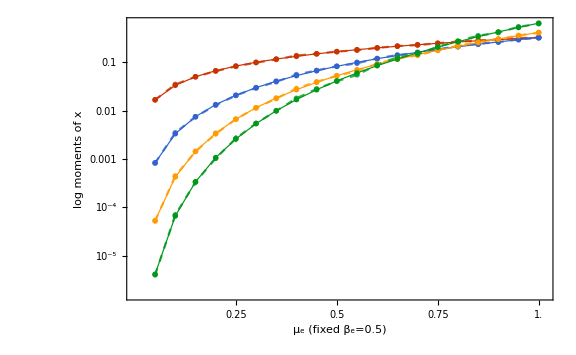

```mathematica
gMomentsCompareVaryWeightsLog=ListLogPlot[
Table[Splice[{
momentsVaryWeightsTheory1[[All,2,m]],
Around/@(momentsVaryWeightsSimulation1[[All,m]])
}],{m,1,4}],
PlotRange->{{0,20.3},All},
FrameLabel->{"μ_e (fixed β_e=0.5)",StyledString["log moments of `math{`it{x}}"]},
FrameTicks->{{None,All},{Table[{i,i/20.},{i,5,20,5}],None}},
PlotStyle->{
{Thickness[0.0015],ColorData[112][1]},{Dashed,Opacity[0.8],ColorData[112][1]},
{Thickness[0.0015],ColorData[112][2]},{Dashed,Opacity[0.8],ColorData[112][2]},
{Thickness[0.0015],ColorData[112][3]},{Dashed,Opacity[0.8],ColorData[112][3]},
{Thickness[0.0015],ColorData[112][4]},{Dashed,Opacity[0.8],ColorData[112][4]}
},
Joined->True,
(*PlotLegends->StyledString/@{
"Simulated `math{E(x^1)}","Theoretical `math{E(x^1)}",
"Simulated `math{E(x^2)}","Theoretical `math{E(x^2)}",
"Simulated `math{E(x^3)}","Theoretical `math{E(x^3)}",
"Simulated `math{E(x^4)}","Theoretical `math{E(x^4)}"
},*)
ImageSize->Large
]
```

```mathematica
gMomentsCompareVaryBoth=ResourceFunction["PlotGrid"][{
{gMomentsCompareVaryRates,gMomentsCompareVaryWeights},
{gMomentsCompareVaryRatesLog,gMomentsCompareVaryWeightsLog}
},ImageSize->800]
savePNG[gMomentsCompareVaryBoth];
```

-Graphics-

```mathematica
testRates3=Table[r,{r,1,100000,5000}];
testWeights3=Table[w,{w,2,30,2}];
```

```mathematica
momentsVaryRatesSimulation3=Table[SingleNeuronSimulationMomentsOfXTrials[τ,h,a,{r},{0.5},5000,15,6],{r,testRates3}];
```

```mathematica
momentsVaryWeightsSimulation3=Table[SingleNeuronSimulationMomentsOfXTrials[τ,h,a,{0.5},{w},3000,15,6],{w,testWeights3}];
```

```mathematica
sims=Map[Mean,momentsVaryWeightsSimulation3,{2}];
Table[(a 2)^k/(k!)sims[[-2]][[k]],{k,1,14}]
```

{0.36593,0.880123,1.48307,1.96516,2.21185,2.25375,2.19257,2.10602,2.01085,1.88462,1.70459,1.47047,1.20419,0.93688}

```mathematica
xx=calcMomentsOfBeta[#,1]&/@Map[Around,momentsVaryWeightsSimulation3,{2}]
```

{0.6810.006,0.82200.0027,0.9370.008,0.9740.009,0.9950.009,1.0140.010,1.0130.010,0.9820.006,0.9810.008,0.9860.008,0.9640.007,0.9260.010,0.8760.005,0.8260.004,0.78430.0032,0.7430.007,0.6840.004,0.64240.0016,0.61090.0035,0.57740.0013}

```mathematica
gMomentsOfBetaCompareVaryRates=ListPlot[
{
calcMomentsOfBeta[#,1]&/@Map[Around,momentsVaryRatesSimulation3,{2}],
(*calcMomentsOfBeta[#,2]&/@Map[Around,momentsVaryRatesSimulation3,{2}],*)
Sqrt[calcMomentsOfBeta[#,2]-calcMomentsOfBeta[#,1]^2]&/@Map[Around,momentsVaryRatesSimulation3,{2}]
},
PlotRange->All,
FrameLabel->{"β_e (fixed μ_e=0.5)",StyledString["second moments of `math{`it{β}}"]},
FrameTicks->{{Automatic,None},{Table[{i,i*5000.},{i,5,20,5}],None}},
PlotStyle->{
{ColorData[112][1]},{ColorData[112][2]}
},
(*PlotLegends->StyledString/@{
"Simulated `math{E(x^1)}","Theoretical `math{E(x^1)}",
"Simulated `math{E(x^2)}","Theoretical `math{E(x^2)}",
"Simulated `math{E(x^3)}","Theoretical `math{E(x^3)}",
"Simulated `math{E(x^4)}","Theoretical `math{E(x^4)}"
},*)
ImageSize->Large
]
```

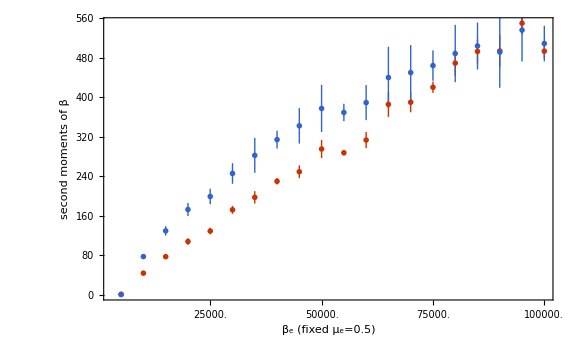

```mathematica
S
```

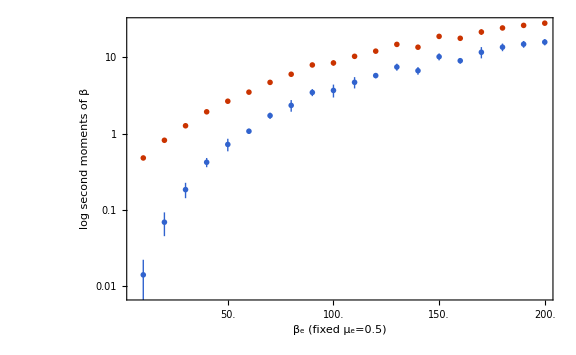

```mathematica
gMomentsOfBetaCompareVaryRatesLog=ListLogPlot[
{
calcMomentsOfBeta[#,2]&/@Map[Around,momentsVaryRatesSimulation3,{2}],
Sqrt[calcMomentsOfBeta[#,2]-calcMomentsOfBeta[#,1]^2]&/@Map[Around,momentsVaryRatesSimulation3,{2}]^2
},
PlotRange->All,
FrameLabel->{"β_e (fixed μ_e=0.5)",StyledString["log second moments of `math{`it{β}}"]},
FrameTicks->{{Automatic,None},{Table[{i,i*10.},{i,5,20,5}],None}},
PlotStyle->{
{ColorData[112][1]},{ColorData[112][2]}
},
(*PlotLegends->StyledString/@{
"Simulated `math{E(x^1)}","Theoretical `math{E(x^1)}",
"Simulated `math{E(x^2)}","Theoretical `math{E(x^2)}",
"Simulated `math{E(x^3)}","Theoretical `math{E(x^3)}",
"Simulated `math{E(x^4)}","Theoretical `math{E(x^4)}"
},*)
ImageSize->Large
]
```

```mathematica
Sqrt[calcMomentsOfBeta[#,2]-calcMomentsOfBeta[#,1]^2]&/@Map[Around,momentsVaryWeightsSimulation3,{2}]
```

{0.0530.014,0.1210.017,0.1960.009,0.2970.008,0.4130.011,0.5330.013,0.6880.012,0.8530.014,1.060.04,1.270.04,1.4510.026,1.6800.032,1.9230.022,2.1960.019,2.590.06}

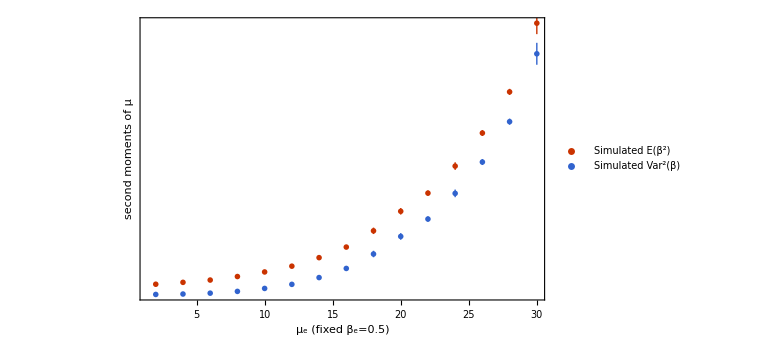

```mathematica
gMomentsOfBetaCompareVaryWeights=ListPlot[
{
calcMomentsOfBeta[#,2]&/@Map[Around,momentsVaryWeightsSimulation3,{2}],
Sqrt[calcMomentsOfBeta[#,2]-calcMomentsOfBeta[#,1]^2]&/@Map[Around,momentsVaryWeightsSimulation3,{2}]^2
},
PlotRange->All,
FrameLabel->{"μ_e (fixed β_e=0.5)",StyledString["second moments of `math{`it{μ}}"]},
FrameTicks->{{None,All},{Table[{i,Floor[i*2]},{i,2.5,15,2.5}],None}},
PlotStyle->{
{ColorData[112][1]},{ColorData[112][2]}
},
PlotLegends->StyledString/@{
"Simulated `math{E(β^2)}","Simulated `math{Var^2(β)}"
},
ImageSize->Large
]
```

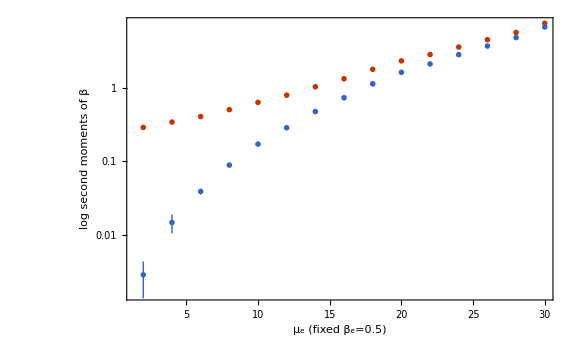

```mathematica
gMomentsOfBetaCompareVaryWeightsLog=ListLogPlot[
{
calcMomentsOfBeta[#,2]&/@Map[Around,momentsVaryWeightsSimulation3,{2}],
Sqrt[calcMomentsOfBeta[#,2]-calcMomentsOfBeta[#,1]^2]&/@Map[Around,momentsVaryWeightsSimulation3,{2}]^2
},
PlotRange->All,
FrameLabel->{"μ_e (fixed β_e=0.5)",StyledString["log second moments of `math{`it{β}}"]},
FrameTicks->{{None,All},{Table[{i,Floor[i*2]},{i,2.5,15,2.5}],None}},
PlotStyle->{
{ColorData[112][1]},{ColorData[112][2]}
},
(*PlotLegends->StyledString/@{
"Simulated `math{E(x^1)}","Theoretical `math{E(x^1)}",
"Simulated `math{E(x^2)}","Theoretical `math{E(x^2)}",
"Simulated `math{E(x^3)}","Theoretical `math{E(x^3)}",
"Simulated `math{E(x^4)}","Theoretical `math{E(x^4)}"
},*)
ImageSize->Large
]
```

```mathematica
gMomentsOfBetaCompareVaryBoth=ResourceFunction["PlotGrid"][{
{gMomentsOfBetaCompareVaryRates,gMomentsOfBetaCompareVaryWeights},
{gMomentsOfBetaCompareVaryRatesLog,gMomentsOfBetaCompareVaryWeightsLog}
},ImageSize->800]
savePNG[gMomentsOfBetaCompareVaryBoth];
```

-Graphics-

```mathematica
testWeights3
```

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30}

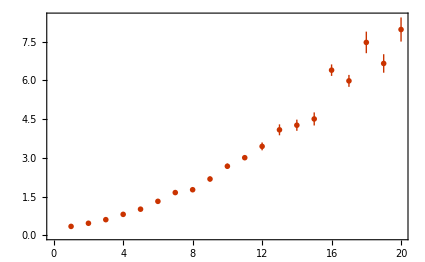

```mathematica
ListPlot[Table[calcMomentsOfBeta[#,q]&/@Map[Around,momentsVaryRatesSimulation3,{2}],{q,2,2}]]
```

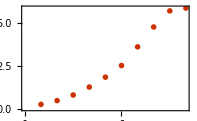

```mathematica
ListPlot[{0.2517038086228153,0.47384549177715996,0.8013358946381286,1.2656264950126133,1.8417833133045551,2.523270744632711,3.616609436544116,4.7759222933050225,5.71617322004409,5.882184789522995}]
```

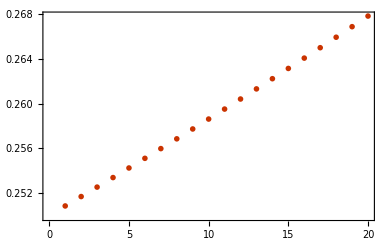

```mathematica
ListPlot[Table[calcMomentsOfBeta[#,q]&/@(momentsVaryWeightsTheory1[[All,2]]),{q,2,2}]]
```

```mathematica
calcMomentsOfBeta
```

```mathematica
testRates2=Table[r,{r,1,30,3}];
testWeights2=Table[w,{w,1,30,3}];
```

```mathematica
momentsVaryRatesSimulation2=Table[SingleNeuronSimulationMomentsOfXTrials[τ,h,a,{r},{0.1},3000,orderUpTo,3],{r,testRates2}];
momentsVaryWeightsSimulation2=Table[SingleNeuronSimulationMomentsOfXTrials[τ,h,a,{0.1},{w},3000,orderUpTo,3],{w,testWeights2}];
```

```mathematica
momentsVaryRatesTheory2=Table[SingleNeuronTheoryMomentOfX[τ,h,a,{r},{0.1},orderUpTo],{r,testRates2}];
momentsVaryWeightsTheory2=Table[SingleNeuronTheoryMomentOfX[τ,h,a,{0.1},{w},orderUpTo],{w,testWeights2}];
```

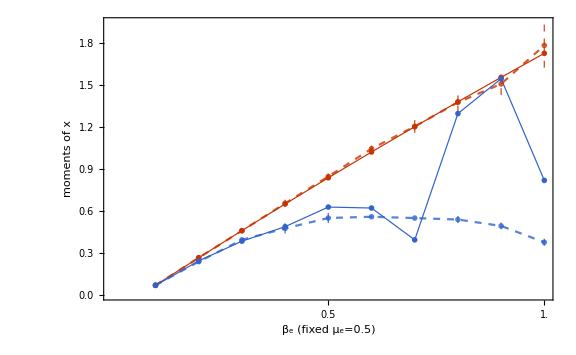

```mathematica
gMomentsCompareVaryRates2=ListLinePlot[
Table[Splice[{
momentsVaryRatesTheory2[[All,2,m]],
Around/@(momentsVaryRatesSimulation2[[All,m]]),
momentsVaryWeightsTheory2[[All,2,m]],
Around/@(momentsVaryWeightsSimulation2[[All,m]])
}],{m,1,1}],
PlotRange->Automatic,
FrameLabel->{"β_e (fixed μ_e=0.5)",StyledString["moments of `math{`it{x}}"]},
FrameTicks->{{Automatic,None},{Table[{i,i/10.},{i,5,30,5}],None}},
PlotStyle->{
{Thickness[0.0015],ColorData[112][1]},{Dashed,Opacity[0.8],ColorData[112][1]},
{Thickness[0.0015],ColorData[112][2]},{Dashed,Opacity[0.8],ColorData[112][2]},
{Thickness[0.0015],ColorData[112][3]},{Dashed,Opacity[0.8],ColorData[112][3]},
{Thickness[0.0015],ColorData[112][4]},{Dashed,Opacity[0.8],ColorData[112][4]}
},
(*PlotLegends->StyledString/@{
"Simulated `math{E(x^1)}","Theoretical `math{E(x^1)}",
"Simulated `math{E(x^2)}","Theoretical `math{E(x^2)}",
"Simulated `math{E(x^3)}","Theoretical `math{E(x^3)}",
"Simulated `math{E(x^4)}","Theoretical `math{E(x^4)}"
},*)
ImageSize->Large
]
savePNG[gMomentsCompareVaryRates2];
```

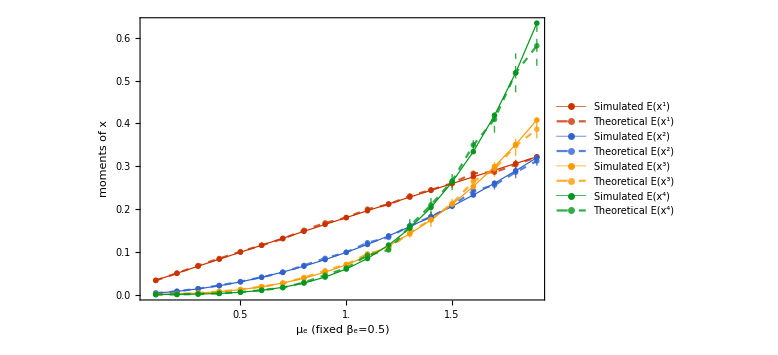

```mathematica
gMomentsCompareVaryWeights=ListLinePlot[
Table[Splice[{
momentsVaryWeightsTheory1[[All,2,m]],
Around/@(momentsVaryWeightsSimulation1[[All,m]])
}],{m,1,4}],
PlotRange->All,
FrameLabel->{"μ_e (fixed β_e=0.5)",StyledString["moments of `math{`it{x}}"]},
FrameTicks->{{Automatic,None},{Table[{i,i/10.},{i,5,30,5}],None}},
PlotStyle->{
{Thickness[0.0015],ColorData[112][1]},{Dashed,Opacity[0.8],ColorData[112][1]},
{Thickness[0.0015],ColorData[112][2]},{Dashed,Opacity[0.8],ColorData[112][2]},
{Thickness[0.0015],ColorData[112][3]},{Dashed,Opacity[0.8],ColorData[112][3]},
{Thickness[0.0015],ColorData[112][4]},{Dashed,Opacity[0.8],ColorData[112][4]}
},
PlotLegends->StyledString/@{
"Simulated `math{E(x^1)}","Theoretical `math{E(x^1)}",
"Simulated `math{E(x^2)}","Theoretical `math{E(x^2)}",
"Simulated `math{E(x^3)}","Theoretical `math{E(x^3)}",
"Simulated `math{E(x^4)}","Theoretical `math{E(x^4)}"
},
ImageSize->Large
]
savePNG[gMomentsCompareVaryWeights]
```

```mathematica
gMomentsCompareVaryBoth=ResourceFunction["PlotGrid"][{{gMomentsCompareVaryRates},{gMomentsCompareVaryWeights}}]
savePNG[gMomentsCompareVaryBoth];
```

-Graphics-

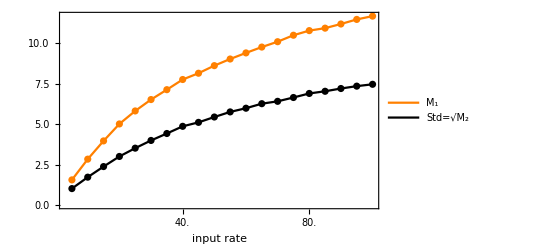

```mathematica
gSecondMomentCompareVaryRates=ListPlot[{simM2XVaryRates[[All,1]],Sqrt[simM2XVaryRates[[All,2]]-simM2XVaryRates[[All,1]]^2]},
PlotRange->All,
Frame->True,
FrameLabel->{"input rate",""},
LabelStyle->Directive[20,Black,FontFamily->"Times"],
FrameTicks->{{Automatic,None},{Table[{i,i*5.},{i,0,20,4}],None}},
PlotStyle->{Orange,Black},
PlotLegends->{"M_1","Std=√M_2"},
Joined->True,
Mesh->All
]
savePNG[gSecondMomentCompareVaryRates]
```

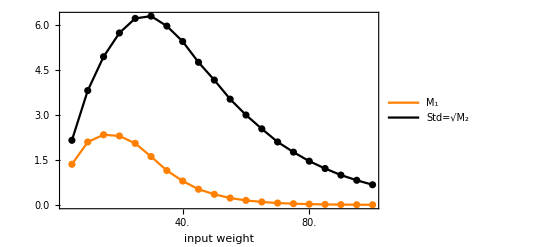

```mathematica
gSecondMomentCompareVaryWeights=ListPlot[{simM2XVaryWeights[[All,1]],Sqrt[simM2XVaryWeights[[All,2]]-simM2XVaryWeights[[All,1]]^2]},
PlotRange->All,
Frame->True,
FrameLabel->{"input weight",""},
LabelStyle->Directive[20,Black,FontFamily->"Times"],
FrameTicks->{{Automatic,None},{Table[{i,i*5.},{i,0,20,4}],None}},
PlotStyle->{Orange,Black},
PlotLegends->{"M_1","Std=√M_2"},
Joined->True,
Mesh->All
]
savePNG[gSecondMomentCompareVaryWeights]
```